```mathematica
pers1:=-1/(8 r^2 c[r]^2)(2c[r]f[r](α c'[r] f'[r]+f[r](α c''[r]-2r c'[r]))+4r c[r]^2 f[r]f'[r]+2κ r^2 c[r]^3(ϵ[r]+p[r])-3α f[r]^2 c'[r]^2)
pers2:=1/(4 r^2 c[r]^2)(-α c[r] f[r] (f[r]c''[r]+c'[r]f'[r])-2 c[r]^2 f[r](r f'[r]+f[r])+c[r]^3(2-κ r^2 (ϵ[r]-p[r]))+α f[r]^2 c'[r]^2)
```

```mathematica
Solve[pers1==0,p[r]]
```

{{p[r]→1/(2 r^2 κ c[r]^3)(-2 r^2 κ c[r]^3 ϵ[r]+4 r c[r] f[r]^2 c'[r]+3 α f[r]^2 c'[r]^2-4 r c[r]^2 f[r] f'[r]-2 α c[r] f[r] c'[r] f'[r]-2 α c[r] f[r]^2 c''[r])}}

```mathematica
Solve[pers2==0,p[r]]
```

{{p[r]→1/(r^2 κ c[r]^3)(-2 c[r]^3+2 c[r]^2 f[r]^2+r^2 κ c[r]^3 ϵ[r]-α f[r]^2 c'[r]^2+2 r c[r]^2 f[r] f'[r]+α c[r] f[r] c'[r] f'[r]+α c[r] f[r]^2 c''[r])}}

```mathematica
Solve[1/(2 r^2 κ c[r]^3)(-2 r^2 κ c[r]^3 ϵ[r]+4 r c[r] f[r]^2 c'[r]+3 α f[r]^2 c'[r]^2-4 r c[r]^2 f[r] f'[r]-2 α c[r] f[r] c'[r] f'[r]-2 α c[r] f[r]^2 c''[r])==1/(r^2 κ c[r]^3)(-2 c[r]^3+2 c[r]^2 f[r]^2+r^2 κ c[r]^3 ϵ[r]-α f[r]^2 c'[r]^2+2 r c[r]^2 f[r] f'[r]+α c[r] f[r] c'[r] f'[r]+α c[r] f[r]^2 c''[r]),ϵ[r]]
```

{{ϵ[r]→1/(4 r^2 κ c[r]^3)(4 c[r]^3-4 c[r]^2 f[r]^2+4 r c[r] f[r]^2 c'[r]+5 α f[r]^2 c'[r]^2-8 r c[r]^2 f[r] f'[r]-4 α c[r] f[r] c'[r] f'[r]-4 α c[r] f[r]^2 c''[r])}}

```mathematica
subs3:=f[r]->√(c[r](1-(2G m[r])/r))
```

```mathematica
(κ ϵ[r]->1/(4 r^2 κ c[r]^3)(4 c[r]^3-4 c[r]^2 f[r]^2+4 r c[r] f[r]^2 c'[r]+5 α f[r]^2 c'[r]^2-8 r c[r]^2 f[r] f'[r]-4 α c[r] f[r] c'[r] f'[r]-4 α c[r] f[r]^2 c''[r]))/.{D[subs3,r]}/.{subs3}
```

κ ϵ[r]→1/(4 r^2 κ c[r]^3)(4 c[r]^3-4 c[r]^3 (1-(2 G m[r])/r)+4 r c[r]^2 (1-(2 G m[r])/r) c'[r]+5 α c[r] (1-(2 G m[r])/r) c'[r]^2-4 r c[r]^2 ((1-(2 G m[r])/r) c'[r]+c[r] ((2 G m[r])/r^2-(2 G m'[r])/r))-2 α c[r] c'[r] ((1-(2 G m[r])/r) c'[r]+c[r] ((2 G m[r])/r^2-(2 G m'[r])/r))-4 α c[r]^2 (1-(2 G m[r])/r) c''[r])

```mathematica
persκϵ:=1/(4 r^2 c[r]^3)(4 c[r]^3-4 c[r]^3 (1-(2 G m[r])/r)+4 r c[r]^2 (1-(2 G m[r])/r) c'[r]+5 α c[r] (1-(2 G m[r])/r) c'[r]^2-4 r c[r]^2 ((1-(2 G m[r])/r) c'[r]+c[r] ((2 G m[r])/r^2-(2 G m'[r])/r))-2 α c[r] c'[r] ((1-(2 G m[r])/r) c'[r]+c[r] ((2 G m[r])/r^2-(2 G m'[r])/r))-4 α c[r]^2 (1-(2 G m[r])/r) c''[r])
```

```mathematica
Simplify[persκϵ+(-(2 G m'[r])/r^2+α/r^2(-(1-(2 G m[r])/r) (3 c'[r]^2)/(4  c[r]^2)-c'[r]/c[r] D[(G m[r])/r,r]+c''[r]/c[r](1-(2 G m[r])/r)))==  0 ]
```

True

Di Carballo-Rubio,
κ ϵ[r]+(-(2 G m'[r])/r^2+α/r^2(-(1-(2 G m[r])/r) (3 c'[r]^2)/(4  c[r]^2)-c'[r]/c[r] D[(G m[r])/r,r]+c''[r]/c[r](1-(2 G m[r])/r)))==0 
jadi sesuai!

```mathematica
Solve[pers1==0,ϵ[r]]
```

{{ϵ[r]→1/(2 r^2 κ c[r]^3)(-2 r^2 κ c[r]^3 p[r]+4 r c[r] f[r]^2 c'[r]+3 α f[r]^2 c'[r]^2-4 r c[r]^2 f[r] f'[r]-2 α c[r] f[r] c'[r] f'[r]-2 α c[r] f[r]^2 c''[r])}}

```mathematica
Solve[pers2==0,ϵ[r]]
```

{{ϵ[r]→1/(r^2 κ c[r]^3)(2 c[r]^3-2 c[r]^2 f[r]^2+r^2 κ c[r]^3 p[r]+α f[r]^2 c'[r]^2-2 r c[r]^2 f[r] f'[r]-α c[r] f[r] c'[r] f'[r]-α c[r] f[r]^2 c''[r])}}

```mathematica
Solve[1/(2 r^2 κ c[r]^3)(-2 r^2 κ c[r]^3 p[r]+4 r c[r] f[r]^2 c'[r]+3 α f[r]^2 c'[r]^2-4 r c[r]^2 f[r] f'[r]-2 α c[r] f[r] c'[r] f'[r]-2 α c[r] f[r]^2 c''[r])==1/(r^2 κ c[r]^3)(2 c[r]^3-2 c[r]^2 f[r]^2+r^2 κ c[r]^3 p[r]+α f[r]^2 c'[r]^2-2 r c[r]^2 f[r] f'[r]-α c[r] f[r] c'[r] f'[r]-α c[r] f[r]^2 c''[r]),p[r]]//Simplify
```

{{p[r]→(-4 c[r]^3+4 c[r]^2 f[r]^2+4 r c[r] f[r]^2 c'[r]+α f[r]^2 c'[r]^2)/(4 r^2 κ c[r]^3)}}

```mathematica
(κ p[r]->(-4 c[r]^3+4 c[r]^2 f[r]^2+4 r c[r] f[r]^2 c'[r]+α f[r]^2 c'[r]^2)/(4 r^2 c[r]^3))/.{D[subs3,r]}/.{subs3}//Simplify//Expand
```

κ p[r]→-(2 G m[r])/r^3+c'[r]/(r c[r])-(2 G m[r] c'[r])/(r^2 c[r])+(α c'[r]^2)/(4 r^2 c[r]^2)-(G α m[r] c'[r]^2)/(2 r^3 c[r]^2)

```mathematica
persκp:=-(2 G m[r])/r^3+c'[r]/(r c[r])-(2 G m[r] c'[r])/(r^2 c[r])+(α c'[r]^2)/(4 r^2 c[r]^2)-(G α m[r] c'[r]^2)/(2 r^3 c[r]^2)
```

```mathematica
Simplify[persκp==(1-(2 G m[r])/r)c'[r]/(r c[r])-(2G m[r])/r^3+(1-(2 G m[r])/r)α/(4 r^2)c'[r]^2/c[r]^2]
```

True

Dari Carballo-Rubio
κ p[r]==(1-(2 G m[r])/r)c'[r]/(r c[r])-(2G m[r])/r^3+(1-(2 G m[r])/r)α/(4 r^2)c'[r]^2/c[r]^2
sudah sesuai juga!

```mathematica
Solve[Simplify[pers1-pers2]==0,f[r]]
```

{{f[r]→-(2 √(c[r]^3+r^2 κ c[r]^3 p[r]))/(√(4 c[r]^2+4 r c[r] c'[r]+α c'[r]^2))},{f[r]→(2 √(c[r]^3+r^2 κ c[r]^3 p[r]))/(√(4 c[r]^2+4 r c[r] c'[r]+α c'[r]^2))}}

```mathematica
subs4:=f[r]->(2 √(c[r]+r^2 κ c[r] p[r]))/(√(4+4 r  c'[r]/c[r]+α (c'[r]/c[r])^2))
subs5:=c[r]->Exp[ν[r]]
```

```mathematica
D[subs5,r]
D[subs5,{r,2}]
```

c'[r]→ⅇ^ν[r] ν'[r]

c''[r]→ⅇ^ν[r] ν'[r]^2+ⅇ^ν[r] ν''[r]

```mathematica
0==pers1/.{subs4}/.{D[subs4,r]}/.{subs5}/.{D[subs5,r]}/.{D[subs5,{r,2}]}//Simplify
```

(ⅇ^ν[r] (r^2 κ ϵ[r] (4+4 r ν'[r]+α ν'[r]^2)^2+2 (r^2 κ p'[r] (8 r+4 (2 r^2+α) ν'[r]+6 r α ν'[r]^2+α^2 ν'[r]^3)-2 (8 r ν'[r]+2 (2 r^2+α) ν'[r]^2+r α ν'[r]^3+4 (r^2-α) ν''[r]))+r κ p[r] (16 (2 r^2+α) ν'[r]+24 r α ν'[r]^2+4 α (r^2+α) ν'[r]^3+r α^2 ν'[r]^4+16 r (3+(-r^2+α) ν''[r]))))/(r (4+4 r ν'[r]+α ν'[r]^2))==0

```mathematica
0==pers2/.{subs4}/.{D[subs4,r]}/.{subs5}/.{D[subs5,r]}/.{D[subs5,{r,2}]}//Simplify
```

(ⅇ^ν[r] (r^2 κ ϵ[r] (4+4 r ν'[r]+α ν'[r]^2)^2+2 (r^2 κ p'[r] (8 r+4 (2 r^2+α) ν'[r]+6 r α ν'[r]^2+α^2 ν'[r]^3)-2 (8 r ν'[r]+2 (2 r^2+α) ν'[r]^2+r α ν'[r]^3+4 (r^2-α) ν''[r]))+r κ p[r] (16 (2 r^2+α) ν'[r]+24 r α ν'[r]^2+4 α (r^2+α) ν'[r]^3+r α^2 ν'[r]^4+16 r (3+(-r^2+α) ν''[r]))))/(r (4+4 r ν'[r]+α ν'[r]^2))==0

```mathematica
Collect[(r^2 κ ϵ[r] (4+4 r ν'[r]+α ν'[r]^2)^2+2 (r^2 κ p'[r] (8 r+4 (2 r^2+α) ν'[r]+6 r α ν'[r]^2+α^2 ν'[r]^3)-2 (8 r ν'[r]+2 (2 r^2+α) ν'[r]^2+r α ν'[r]^3+4 (r^2-α) ν''[r]))+r κ p[r] (16 (2 r^2+α) ν'[r]+24 r α ν'[r]^2+4 α (r^2+α) ν'[r]^3+r α^2 ν'[r]^4+16 r (3+(-r^2+α) ν''[r])))//Simplify,{ν'[r],ν''[r]}]
```

48 r^2 κ p[r]+16 r^2 κ ϵ[r]+16 r^3 κ p'[r]+(-32 r+16 r (2 r^2+α) κ p[r]+32 r^3 κ ϵ[r]+8 r^2 (2 r^2+α) κ p'[r]) ν'[r]+(-8 (2 r^2+α)+24 r^2 α κ p[r]+16 r^4 κ ϵ[r]+8 r^2 α κ ϵ[r]+12 r^3 α κ p'[r]) ν'[r]^2+(-4 r α+4 r α (r^2+α) κ p[r]+8 r^3 α κ ϵ[r]+2 r^2 α^2 κ p'[r]) ν'[r]^3+(r^2 α^2 κ p[r]+r^2 α^2 κ ϵ[r]) ν'[r]^4+(-16 (r^2-α)+16 r^2 (-r^2+α) κ p[r]) ν''[r]

```mathematica
Collect[48 r^2 κ p[r]+16 r^2 κ ϵ[r]+16 r^3 κ p'[r]+(-32 r+16 r (2 r^2+α) κ p[r]+32 r^3 κ ϵ[r]+8 r^2 (2 r^2+α) κ p'[r]) ν'[r]+(-8 (2 r^2+α)+24 r^2 α κ p[r]+16 r^4 κ ϵ[r]+8 r^2 α κ ϵ[r]+12 r^3 α κ p'[r]) ν'[r]^2+(-4 r α+4 r α (r^2+α) κ p[r]+8 r^3 α κ ϵ[r]+2 r^2 α^2 κ p'[r]) ν'[r]^3+(r^2 α^2 κ p[r]+r^2 α^2 κ ϵ[r]) ν'[r]^4+(-16 (r^2-α)+16 r^2 (-r^2+α) κ p[r]) ν''[r]/.{ν[r]->2ρ[r]}/.{ν'[r]->2ρ'[r]}/.{ν''[r]->2ρ''[r]}/.{ϵ[r]->m[r]}//Simplify,{ρ'[r],ρ''[r]}]
```

16 (r^2 κ m[r]+3 r^2 κ p[r]+r^3 κ p'[r])+16 r (-4+4 r^2 κ m[r]+2 (2 r^2+α) κ p[r]+r (2 r^2+α) κ p'[r]) ρ'[r]+16 (-4 r^2-2 α+2 r^2 (2 r^2+α) κ m[r]+6 r^2 α κ p[r]+3 r^3 α κ p'[r]) ρ'[r]^2+16 r α (-2+4 r^2 κ m[r]+2 (r^2+α) κ p[r]+r α κ p'[r]) ρ'[r]^3+16 r^2 α^2 κ (m[r]+p[r]) ρ'[r]^4-32 (r^2-α) (1+r^2 κ p[r]) ρ''[r]

Pers 5.7 - 5.10 di [Ho & Matsuo, JHEP03 (2018) 096] sudah terkonfirmasi benar sama dengan pers 7 & 8 di [Carballo-Rubio, PRL 120, 061102 (2018)]

```mathematica
subs6:=p[r]->-m0+p0 Exp[-ρ[r]]
subs7:=m[r]-> m0
```

```mathematica
Collect[((16 (r^2 κ m[r]+3 r^2 κ p[r]+r^3 κ p'[r])+16 r (-4+4 r^2 κ m[r]+2 (2 r^2+α) κ p[r]+r (2 r^2+α) κ p'[r]) ρ'[r]+16 (-4 r^2-2 α+2 r^2 (2 r^2+α) κ m[r]+6 r^2 α κ p[r]+3 r^3 α κ p'[r]) ρ'[r]^2+16 r α (-2+4 r^2 κ m[r]+2 (r^2+α) κ p[r]+r α κ p'[r]) ρ'[r]^3+16 r^2 α^2 κ (m[r]+p[r]) ρ'[r]^4-32 (r^2-α) (1+r^2 κ p[r]) ρ''[r])/.{D[subs6,r]}/.{subs6}/.{subs7})/(16 ⅇ^(-ρ[r])),{ρ'[r],ρ''[r]}]//Simplify
```

-(2 ⅇ^ρ[r] m0-3 p0) r^2 κ-r (-p0 (3 r^2+2 α) κ+2 ⅇ^ρ[r] (2+m0 α κ)) ρ'[r]+(p0 r^2 (-2 r^2+5 α) κ+ⅇ^ρ[r] (-2 α+4 m0 r^4 κ-4 r^2 (1+m0 α κ))) ρ'[r]^2+r α (-p0 (r^2-2 α) κ+2 ⅇ^ρ[r] (-1+m0 (r^2-α) κ)) ρ'[r]^3+2 (r^2-α) (-p0 r^2 κ+ⅇ^ρ[r] (-1+m0 r^2 κ)) ρ''[r]

Pakai koodinat tortoise

```mathematica
pers10:=-1/(8 r[rs]^2)(2(α ν''[rs]-2 r[rs] ν'[rs] r'[rs])+4 r[rs] r''[rs]+2κ r[rs]^2 p0 Exp[ν[rs]/2]-α ν'[rs]^2)
pers20:=1/(4 r[rs]^2)(-α ν''[rs]-2(r[rs] r''[rs]+r'[rs]^2)+Exp[ν[rs]](2-κ r[rs]^2(2ρ0-p0 Exp[-ν[rs]/2])))
```

Sudah sesuai, karena

```mathematica
-4 r[rs]^2 pers10/.{ν[rs]->2ρ[rs],ν'[rs]->2ρ'[rs],ν''[rs]->2ρ''[rs]}//Simplify
```

ⅇ^ρ[rs] p0 κ r[rs]^2+r[rs] (-4 r'[rs] ρ'[rs]+2 r''[rs])+2 α (-ρ'[rs]^2+ρ''[rs])

```mathematica
4 r[rs]^2 pers20/.{ν[rs]->2ρ[rs],ν'[rs]->2ρ'[rs],ν''[rs]->2ρ''[rs]}//Simplify//Expand
```

2 ⅇ^(2 ρ[rs])+ⅇ^ρ[rs] p0 κ r[rs]^2-2 ⅇ^(2 ρ[rs]) κ ρ0 r[rs]^2-2 r'[rs]^2-2 r[rs] r''[rs]-2 α ρ''[rs]

Cari bentuk untuk dimasukkan ke fortran

```mathematica
Solve[pers10==0,ν''[rs]]//Simplify
```

{{ν''[rs]→(-2 ⅇ^(ν[rs]/2) p0 κ r[rs]^2+α ν'[rs]^2+4 r[rs] (r'[rs] ν'[rs]-r''[rs]))/(2 α)}}

```mathematica
Solve[pers20==0,r''[rs]]//Simplify
```

{{r''[rs]→(2 ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-2 ⅇ^ν[rs] κ ρ0) r[rs]^2-2 r'[rs]^2-α ν''[rs])/(2 r[rs])}}

```mathematica
r''[rs]->(2 ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-2 ⅇ^ν[rs] κ ρ0) r[rs]^2-2 r'[rs]^2-α ν''[rs])/(2 r[rs])/.{ν''[rs]->(-2 ⅇ^(ν[rs]/2) p0 κ r[rs]^2+α ν'[rs]^2+4 r[rs] (r'[rs] ν'[rs]-r''[rs]))/(2 α)}//Simplify
```

r''[rs]→(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]-r'[rs] ν'[rs]+(ⅇ^ν[rs]-r'[rs]^2-1/4 α ν'[rs]^2)/r[rs]+r''[rs]

Tortoise coord.

```mathematica
Solve[rs==R+a0 Log[R/a0-1],R]
```

{{R→a0 (1+ProductLog[ⅇ^(-1+rs/a0)])}}

```mathematica
D[Log[√(1-a0/r[rs])],rs]

%/.{r'[rs]->1-a0/r[rs]}
```

(a0 r'[rs])/(2 (1-a0/r[rs]) r[rs]^2)

a0/(2 r[rs]^2)

Ganti bentuk pers gerak, bisa mirip hasil di paper untuk empty space

```mathematica
pers10:=-1/(8 r[rs]^2)(2(α ν''[rs]-2 r[rs] ν'[rs] r'[rs])+4 r[rs] r''[rs]+2κ r[rs]^2 p0 Exp[ν[rs]/2]-α ν'[rs]^2)
pers20:=1/(4 r[rs]^2)(-α ν''[rs]-2(r[rs] r''[rs]+r'[rs]^2)+Exp[ν[rs]](2-κ r[rs]^2(2ρ0-p0 Exp[-ν[rs]/2])))
```

```mathematica
8 r[rs]^2(pers10-pers20)//Simplify
```

-4 ⅇ^ν[rs]+(-4 ⅇ^(ν[rs]/2) p0 κ+4 ⅇ^ν[rs] κ ρ0) r[rs]^2+4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+α ν'[rs]^2

```mathematica
8 r[rs]^2(pers10+pers20)//Simplify
```

4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+α ν'[rs]^2+4 r[rs] (r'[rs] ν'[rs]-2 r''[rs])-4 α ν''[rs]

```mathematica
Clear["Global`*"];

persν:=-4 ⅇ^ν[rs]+(-4 ⅇ^(ν[rs]/2) p0 κ+4 ⅇ^ν[rs] κ ρ0) r[rs]^2+4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+α ν'[rs]^2==0
persr:=4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+α ν'[rs]^2+4 r[rs] (r'[rs] ν'[rs]-2 r''[rs])-4 α ν''[rs]==0

(*G=1.323790281083862 10^-12;
ms=1.1154605324408694 10^15;
planck length= 1.616 10^-35 m*)
l=√(5.* 10.^-2);
α=l^2;
κ =1;
ρ0=0./κ;
a0:=10.
(*M=a0/(2G);*)
R=x/.Solve[400.==x+a0 Log[x/a0-1],x][[1]];
r0=R+a0 Log[R/a0-1];
rn=-10.^4;
ν0=Log[1-a0/R];
ν01a=a0/R^2;
ν01b=α/(2 √(α Log[((R^2-α)/(a0^2-α))]));
ν01c=-α/(2 √(α Log[((r0^2-α)/(a0^2-α))]));
ν01=ν01a;
p0=ρ0 Exp[ν0/2];
-ρ0+p0 Exp[-ν0/2]//N
N[{κ ρ0,r0,a0,α}]
N[{r0,rn,R}]
N[{ν[r0]==ν0,ν'[r0]==ν01,r[r0]==R,r'[r0]==(1-a0/R)}]
```

0.

{0.,400.,10.,0.05}

{400.,-10000.,364.324}

{ν[400.]==-0.0278319,ν'[400.]==0.0000753399,r[400.]==364.324,r'[400.]==0.972552}

```mathematica
s=NDSolve[{persν,persr,ν[r0]==ν0,ν'[r0]==ν01,r[r0]==R,r'[r0]==(1-a0/R),WhenEvent[r[rs]==a0,{rbs=rs,"StopIntegration"}]},{ν,r},{rs,r0,rn}]
νo[rs_]=Evaluate[ν[rs]/.s][[1]];
ro[rs_]=Evaluate[r[rs]/.s][[1]];
(*rbs*)
```

{{ν→InterpolatingFunction[{{-3865.44, 400.}}, <>],r→InterpolatingFunction[{{-3865.44, 400.}}, <>]}}

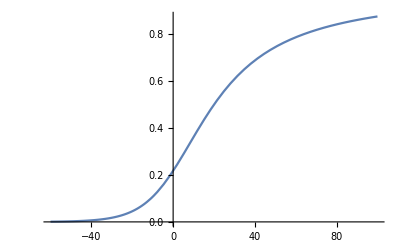

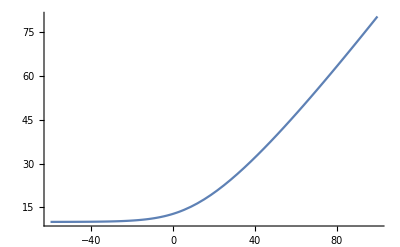

```mathematica
rnn:=-60
r00:=100
Plot[Exp[νo[rs]],{rs,rnn,r00}]
Plot[ro[rs],{rs,rnn,r00}]
```

```mathematica
FindMinimum[ro[x],x]
```

{10.0131,{x→-79.8789}}

```mathematica
?FindMinimum
```

RowBox[{"FindMinimum", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["x", "TI"]}], "]"}] searches for a local minimum in StyleBox["f", "TI"], starting from an automatically selected point.
RowBox[{"FindMinimum", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}]}], "]"}] searches for a local minimum in StyleBox["f", "TI"], starting from the point RowBox[{StyleBox["x", "TI"], "=", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}]. 
RowBox[{"FindMinimum", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] searches for a local minimum in a function of several variables. 
RowBox[{"FindMinimum", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] searches for a local minimum subject to the constraints StyleBox["cons", "TI"].
RowBox[{"FindMinimum", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] starts from a point within the region defined by the constraints.

Coba bentuk piecewise

```mathematica
Clear["Global`*"];

persν:=-4 ⅇ^ν[rs]+(-4 ⅇ^(ν[rs]/2) p0 κ+4 ⅇ^ν[rs] κ ρ0[rs]) r[rs]^2+4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+α ν'[rs]^2==0
persr:=4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0[rs] r[rs]^2-4 r'[rs]^2+α ν'[rs]^2+4 r[rs] (r'[rs] ν'[rs]-2 r''[rs])-4 α ν''[rs]==0

(*G=1.323790281083862 10^-12;
ms=1.1154605324408694 10^15;
planck length= 1.616 10^-35 m*)
l=√(5.* 10.^-2);
α=l^2;
κ =1;
a0:=10.
(*M=a0/(2G);*)
R=x/.Solve[-60.==x+a0 Log[x/a0-1],x][[1]];
r0=R+a0 Log[R/a0-1];
rn=-10.^3;
ν0=Log[1-a0/R];
ν01a=a0/R^2;
ν01=ν01a;
ρ0[rs_]=Piecewise[{{0./κ,rs>y},{25./κ,rs≤y}}]/.{y->-60.};
p0=ρ0[rs] Exp[ν0/2];
N[{κ ρ0[rs],r0,a0,α}]
N[{r0,rn,a0/R,a0/x}/.Solve[-60.==x+a0 Log[x/a0-1],x][[1]]]
N[{ν[r0]==ν0,ν'[r0]==ν01,r[r0]==R,r'[r0]==(1-a0/R)}]
```

{Piecewise[{{0., rs>-60.}, {25., rs≤-60.}, {0., True}}],-60.,10.,0.05}

{-60.,-1000.,0.99909,0.99909}

{ν[-60.]==-7.00182,ν'[-60.]==0.099818,r[-60.]==10.0091,r'[-60.]==0.000910222}

```mathematica
s=NDSolve[{persν,persr,ν[r0]==ν0,ν'[r0]==ν01,r[r0]==R,r'[r0]==(1-a0/R)},{ν,r},{rs,r0,rn}]
νo[rs_]=Evaluate[ν[rs]/.s][[1]];
ro[rs_]=Evaluate[r[rs]/.s][[1]];
(*rbs*)
```

{{ν→InterpolatingFunction[{{-71.5213, -60.}}, <>],r→InterpolatingFunction[{{-71.5213, -60.}}, <>]}}

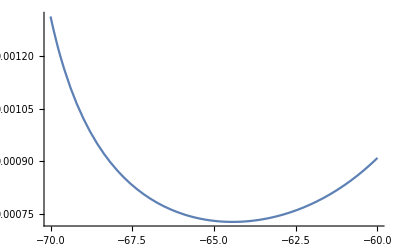

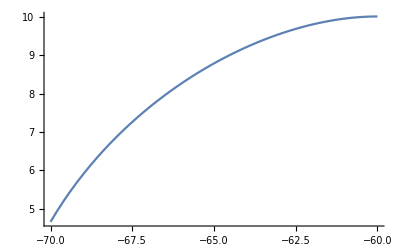

```mathematica
rnn:=-70.
r00:=-60.
Plot[Exp[νo[rs]],{rs,rnn,r00}]
Plot[ro[rs],{rs,rnn,r00}]
```

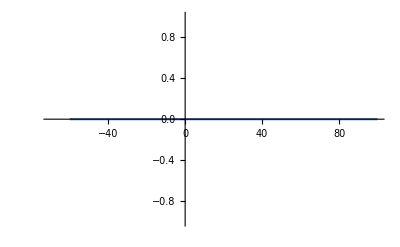

```mathematica
Plot[-ρ0[rs]+p0 Exp[-νo[rs]/2],{rs,rnn,r00}]
```